```mathematica
LV[N_]:=Binomial[x,2](1/N)Product[(N-i)/N,{i,1,x-2}] /.x->56
```

```mathematica
tV=Table[N@LV[n],{n,5,10000,10}];
```

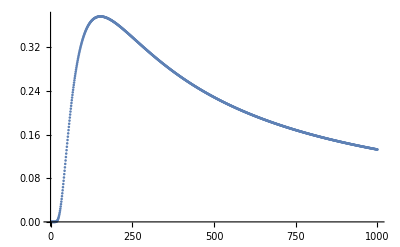

```mathematica
ListPlot[tV]
```

```mathematica
LU[N_]:=Product[(N-i)/N,{i,1,x-1}] /.x->24
```

```mathematica
tU=Table[N@LU[n],{n,5,10000,10}];
```

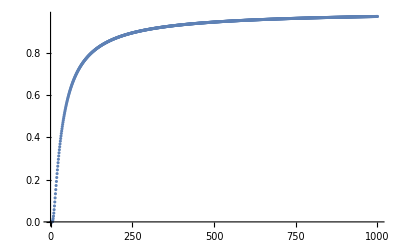

```mathematica
ListPlot[tU]
```

```mathematica
vals=Sum[Table[If[DuplicateFreeQ[Table[RandomInteger[{1,2000}],{i,x}]],1,0],{x,1,100}],{i,1000}]
```

{1000,1000,999,997,996,994,988,986,985,975,975,964,962,963,940,946,934,921,925,914,885,871,877,851,866,870,839,824,814,806,816,752,779,766,755,711,719,698,668,675,657,636,621,638,626,602,586,575,548,529,509,538,543,466,471,438,440,439,409,438,401,394,373,358,339,330,322,311,326,314,275,253,251,245,245,241,233,221,219,194,183,205,158,178,172,152,150,132,135,122,132,116,109,117,93,109,87,94,77,84}

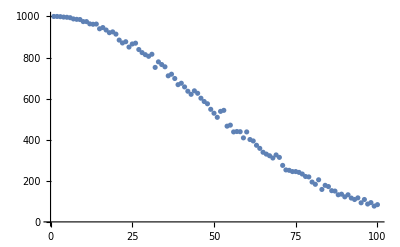

```mathematica
ListPlot[vals]
```